```mathematica
ClearAll["Global`*"];
Remove["Global`*"];
```

```mathematica
hc=Rationalize[0.197327053,0];
rules={T->Rationalize[0.15444512,0],MT->√(M^2+PT^2),M->mρ,mπ->Rationalize[0.13957,0],mρ->Rationalize[0.77580,0],PT->Rationalize[3.69431,0],Y->0,Jρ->1,Jπ->0,Jr->Jρ,ηf->3/5,τ0->5,Δτ->1,R->5,Φ->Rationalize[0,0]};
I1[α_,β_,γ_]:=2((α-I β)BesselK[1,√((α-I β)^2+γ^2)])/(√((α-I β)^2+γ^2));
```

```mathematica
rlim=(15R)/(√(1+MT ηf^2/T))//.rules;
rlim//N
norm=NIntegrate[(MT(2Jr+1))/(π(2π)^3 hc^1 Δτ) r τ Exp[(-(τ-τ0)^2)/(2 Δτ^2)] E^(-r^2/(2 R^2)+(PT/T) Sinh[ηf r/R]Cos[ϕ-Φ]) I1[(MT/T) Cosh[ηf r/R],0,0]//.rules,{ϕ,0,2π},{τ,0,10},{r,0,rlim}]
```

23.9591

0.00055547

```mathematica
Needs["NumericalDifferentialEquationAnalysis`"];
{τpts,τwts}=GaussianQuadratureWeights[31,0,10]//Transpose;
{rpts,rwts}=GaussianQuadratureWeights[31,0,rlim]//Transpose;
{ϕpts,ϕwts}=GaussianQuadratureWeights[31,0,2π]//Transpose;
grid=Flatten[Table[{rpts[[i]],τpts[[j]],ϕpts[[k]],MT/(π(2π)^3 hc^1 Δτ) rpts[[i]] τpts[[j]] Exp[(-(τpts[[j]]-τ0)^2)/(2 Δτ^2)]//.rules,E^(-rpts[[i]]^2/(2 R^2)+(PT/T) Sinh[ηf rpts[[i]]/R]Cos[ϕpts[[k]]-Φ]) //.rules, I1[(MT/T) Cosh[ηf rpts[[i]]/R],0,0]//.rules,rwts[[i]]τwts[[j]]ϕwts[[k]] MT/(π(2π)^3 hc^1 Δτ) rpts[[i]] τpts[[j]] Exp[(-(τpts[[j]]-τ0)^2)/(2 Δτ^2)] E^(-rpts[[i]]^2/(2 R^2)+(PT/T) Sinh[ηf rpts[[i]]/R]Cos[ϕpts[[k]]-Φ]) I1[(MT/T) Cosh[ηf rpts[[i]]/R],0,0]//.rules},{i,Length[rpts]},{j,Length[τpts]},{k,Length[ϕpts]}],2];
```

```mathematica
qo Cos[ϕ]+qs Sin[ϕ]//.{qo->qx Cos[ΦK]+qy Sin[ΦK],qs->qy Cos[ΦK]-qx Sin[ΦK]}//FullSimplify
```

qx Cos[ϕ+ΦK]+qy Sin[ϕ+ΦK]

```mathematica
1/norm NIntegrate[(MT r τ)/(π(2π hc)^3 Δτ) Exp[(-(τ-τ0)^2)/(2 Δτ^2)-I r/hc(qo Cos[ϕ]+qs Sin[ϕ])] E^(-r^2/(2 R^2)+(PT/T) Sinh[ηf r/R]Cos[ϕ-Φ]) I1[(MT/T) Cosh[ηf r/R],τ/hc(qt Cosh[Y]-qz Sinh[Y]),τ/hc(qz Cosh[Y]-qt Sinh[Y])]//.{qt->√(ξ2+qo PT)-√(ξ2-qo PT),ξ2->mπ^2+PT^2+1/4(qo^2+qs^2+qz^2),qx->qo Cos[Φ]-qs Sin[Φ],qy->qs Cos[Φ]+qo Sin[Φ],qo->50/1000,qs->0}~Join~rules,{τ,0,10},{r,0,rlim},{ϕ,0,2π},Method->"GaussKronrodRule"]
1+Abs[%]^2
(*qx->qo Cos[Φ]-qs Sin[Φ],qy->qs Cos[Φ]+qo Sin[Φ]*)
(*{qo->qx Cos[Φ]+qy Sin[Φ],qs->qy Cos[Φ]-qx Sin[Φ]}*)
```

0.425428

```mathematica
1/norm NIntegrate[(2π MT)/(π(2π hc)^3 Δτ)r τ Exp[-(τ-τ0)^2/(2 Δτ^2)-r^2/(2 R^2)] BesselI[0,√(((PT/T Sinh[ηf r/R])^2-(r/hc)^2(qo^2+qs^2))-2I r/hc PT/T Sinh[ηf r/R](qo Cos[Φ]+qs Sin[Φ]))]I1[MT/T Cosh[ηf r/R],τ/hc(qt Cosh[Y]-qz Sinh[Y]),τ/hc(qz Cosh[Y]-qt Sinh[Y])]//.{qt->√(ξ2+qo PT)-√(ξ2-qo PT),ξ2->mπ^2+PT^2+1/4(qo^2+qs^2+qz^2)}~Join~rules~Join~{qx->50/1000,qy->0,qo->qx Cos[ΦK]+qy Sin[ΦK],qs->qy Cos[ΦK]-qx Sin[ΦK]},{τ,0,10},{r,0,rlim},Method->"GaussKronrodRule"]
1+Abs[%]^2
```

0.570159-0.316778 ⅈ

0.42543

Below this line is a direct check of Wiedemann and Heinz’ results

Direct

```mathematica
ClearAll["Global`*"];
Remove["Global`*"];
```

```mathematica
hc=Rationalize[0.197327053,0];
rules={T->Rationalize[0.15444512,0],MT->√(M^2+PT^2),M->mπ,mπ->Rationalize[0.13957,0],mρ->Rationalize[0.7758,0],PT->Rationalize[3.69431,0],τ0->5,Y->0,ηf->3/5,R->5,Jπ->0,Jρ->1,Jr->Jπ};
```

```mathematica
normD=NIntegrate[(2 (2Jr+1)MT τ0 r)/(π(2π)^(3/2)hc) Exp[-r^2/(2 R^2)]BesselK[1,MT/T Cosh[ηf r/R]]BesselI[0,PT/T Sinh[ηf r/R]] //.rules,{r,0,∞}]
```

0.000691612

Resonances

```mathematica
I1[α_,β_,γ_]:=2((α-I β)BesselK[1,√((α-I β)^2+γ^2)])/(√((α-I β)^2+γ^2));
rules={T->Rationalize[0.15444512,0],PT->√(MT^2-M^2),mT->√(mπ^2+pT^2),M->Rationalize[0.7758,0],Γ->Rationalize[0.1503,0],mπ->Rationalize[0.13957,0],mπ0->Rationalize[0.13498,0],y->0,b->1,pT->Rationalize[3.69431,0],ηf->3/5,τ0->5,R->5,m2->mπ0,Jr->Jρ,Jρ->1,Jπ->0,MTbar->(es M mT Cosh[Y-y])/(mT^2 Cosh[Y-y]^2-pT^2),ps->(√(((M+mπ)^2-m2^2)((M-mπ)^2-m2^2)))/(2M),es->√(mπ^2+ps^2),ΔMT->(M pT √(es^2+pT^2-mT^2 Cosh[Y-y]^2))/(mT^2 Cosh[Y-y]^2-pT^2),Y->y+v ΔY,MT->MTbar+ΔMT Cos[ζ],ΔY->Log[ps/mT+√(1+(ps/mT)^2)]};
normR=NIntegrate[(2 MT^2 ΔY(2Jr+1))/(√(mT^2 Cosh[v ΔY]^2-pT^2))((b M)/(4π ps))((2τ0 r)/(π(2π)^(3/2)hc) )Exp[-r^2/(2 R^2)]BesselK[1,MT/T Cosh[ηf r/R]]BesselI[0,PT/T Sinh[ηf r/R]] //.rules,{v,-1,1},{ζ,0,π},{r,0,50}]
integrand[v_,ζ_,r_]:=((2 MT^2 ΔY(2Jr+1))/(√(mT^2 Cosh[v ΔY]^2-pT^2))((b M)/(4π ps))((2τ0 r)/(π(2π)^(3/2)hc) ) Exp[-r^2/(2 R^2)] BesselI[0,PT/T Sinh[ηf r/R]] 1/2 I1[MT/T Cosh[ηf r/R],0,0] //.rules)//Evaluate;
Needs["NumericalDifferentialEquationAnalysis`"];
{vpts,vwts}=GaussianQuadratureWeights[21,-1,1]//Transpose;
{ζpts,ζwts}=GaussianQuadratureWeights[21,0,π]//Transpose;
{rpts,rwts}=GaussianQuadratureWeights[21,0,24]//Transpose;
numR=Sum[rwts[[i]]vwts[[j]]ζwts[[k]]integrand[vpts[[j]],ζpts[[k]],rpts[[i]]],{i,Length[rpts]},{j,Length[vpts]},{k,Length[ζpts]}]
```

0.000138091

0.000137988

```mathematica
{normD,normR,normD+normR}
((25R)/(√(1+mT ηf^2/T))//.rules)//N
```

{0.000691612,0.000138091,0.000829703}

40.3073

```mathematica
(*CHECK 3-body*)
ClearAll["Global`*"];
Remove["Global`*"];
```

```mathematica
hc=Rationalize[0.197327053,0];
(*rules={T->Rationalize[0.15444512,0],MT->√(M^2+PT^2),M->Rationalize[0.7758,0],pT->PT,mT->√(m^2+pT^2),Jr->0,mπ->Rationalize[0.13957,0],PT->Rationalize[0.007177524,0],ηf->3/5,τ0->5,Δτ->1,R->5,Φ->Rationalize[0,0]};I1[α_,β_,γ_]:=2((α-I β)BesselK[1,√((α-I β)^2+γ^2)])/(√((α-I β)^2+γ^2));*)
rules={T->Rationalize[0.15444512,0],MT->√(M^2+PT^2),M->Rationalize[0.7758,0],Jr->1,PT->Rationalize[3.69431427482,0],ηf->3/5,τ0->5,Δτ->1,R->5,Φ->Rationalize[0,0]};
rlim=(15R)/(√(1+MT ηf^2/T))//.rules;
NIntegrate[(2MT τ0 r(2Jr+1))/(π(2π)^(3/2)hc^1) Exp[-r^2/(2 R^2)]BesselK[1,MT/T Cosh[ηf r/R]]BesselI[0,PT/T Sinh[ηf r/R]]HeavisideTheta[700-MT/T Cosh[ηf r/R]] //.rules,{r,0,rlim}]
```

0.000555468

```mathematica
rules={T->Rationalize[0.15444512,0],PT->√(MT^2-M^2),mT->√(mπ^2+pT^2),m2->Rationalize[0.13498,0],M->Rationalize[0.7758,0],Γ->Rationalize[0.1503,0],mπ->Rationalize[0.13957,0],y->0,b->1,pT->Rationalize[0.007177524,0],ηf->3/5,τ0->5,Δτ->1,R->5,Jr->1,MTbar->(es M mT Cosh[Y-y])/(mT^2 Cosh[Y-y]^2-pT^2),ps->(√(((M+mπ)^2-m2^2)((M-mπ)^2-m2^2)))/(2M),es->√(mπ^2+ps^2),ΔMT->(M pT √(es^2+pT^2-mT^2 Cosh[Y-y]^2))/(mT^2 Cosh[Y-y]^2-pT^2),Y->y+v ΔY,MT->MTbar+ΔMT Cos[ζ],ΔY->Log[ps/mT+√(1+(ps/mT)^2)]};
NIntegrate[(2mT τ0 r)/(π(2π)^(3/2)hc^1) Exp[-r^2/(2 R^2)]BesselK[1,mT/T Cosh[ηf r/R]]BesselI[0,pT/T Sinh[ηf r/R]] //.rules,{r,0,65}]
NIntegrate[(2 MT^2 ΔY(2Jr+1))/(√(mT^2 Cosh[v ΔY]^2-pT^2))((b M)/(4π ps))((2τ0 r)/(π(2π)^(3/2)hc) )Exp[-r^2/(2 R^2)]BesselK[1,MT/T Cosh[ηf r/R]]BesselI[0,PT/T Sinh[ηf r/R]] //.rules,{r,0,100},{v,-1,1},{ζ,0,π}]
```

1.61779

0.432411

```mathematica
numD=NIntegrate[(2 MT τ0 r)/(π(2π)^(3/2)hc^1)Exp[-r^2/(2 R^2)]BesselK[1,MT/T Cosh[ηf r/R]]BesselI[0,PT/T Sinh[ηf r/R]] //.rules,{r,0,rlim}]
1+Abs[numD/normD]^2
```

0.0504734-0.0280529 ⅈ

1.42562

```mathematica
rules={T->Rationalize[0.15444512,0],PT->√(MT^2-M^2),mT->√(m^2+pT^2),m->mπ,m2->mπ,m3->Rationalize[0.13498,0],M->Rationalize[0.78259,0],Γ->Rationalize[0.00849,0],mπ->Rationalize[0.13957,0],y->0,b->1,pT->Rationalize[1.01002173,0],ηf->3/5,τ0->5,Δτ->1,R->5,Jr->1,MTbar->(es M mT Cosh[Y-y])/(mT^2 Cosh[Y-y]^2-pT^2),ps->(√(((M+mπ)^2-s)((M-mπ)^2-s)))/(2M),es->√(m^2+ps^2),ΔMT->(M pT √(es^2+pT^2-mT^2 Cosh[Y-y]^2))/(mT^2 Cosh[Y-y]^2-pT^2),Y->y+v ΔY,MT->MTbar+ΔMT Cos[ζ],ΔY->Log[ps/mT+√(1+(ps/mT)^2)]};
Qfunc=NIntegrate[1/s √(((M+m)^2-s)((M-m)^2-s)((m2+m3)^2-s)((m2-m3)^2-s))//.rules,{s,(m2+m3)^2//.rules,(M-m)^2//.rules}];
normR=NIntegrate[(2 MT^2 ΔY(2Jr+1))/(√(mT^2 Cosh[v ΔY]^2-pT^2))((b M)/(2π s Qfunc)√((s-(m2+m3)^2)(s-(m2-m3)^2)))((2τ0 r M)/(π(2π)^(3/2)hc) )Exp[-r^2/(2 R^2)]BesselK[1,MT/T Cosh[ηf r/R]]BesselI[0,PT/T Sinh[ηf r/R]] //.rules,{s,(m2+m3)^2//.rules,(M-m)^2//.rules},{v,-1,1},{ζ,0,π},{r,0,20}]
integrand[s_,v_,ζ_,r_]:=(2 MT^2 ΔY(2Jr+1))/(√(mT^2 Cosh[v ΔY]^2-pT^2))((b M)/(2π s Qfunc)√((s-(m2+m3)^2)(s-(m2-m3)^2)))((2τ0 r M)/(π(2π)^(3/2)hc) ) Exp[-r^2/(2 R^2)] BesselI[0,PT/T Sinh[ηf r/R]]I1[MT/T Cosh[ηf r/R],0,0] //.rules//Evaluate;
Needs["NumericalDifferentialEquationAnalysis`"];
{spts,swts}=GaussianQuadratureWeights[21,(m2+m3)^2//.rules,(M-m)^2//.rules]//Transpose;
{vpts,vwts}=GaussianQuadratureWeights[21,-1,1]//Transpose;
{ζpts,ζwts}=GaussianQuadratureWeights[21,0,π]//Transpose;
{rpts,rwts}=GaussianQuadratureWeights[21,0,50]//Transpose;
numR=Sum[rwts[[i]]swts[[i2]]vwts[[j]]ζwts[[k]]integrand[spts[[i2]],vpts[[j]],ζpts[[k]],rpts[[i]]],{i,Length[rpts]},{j,Length[vpts]},{k,Length[ζpts]},{l,Length[τpts]},{i2,Length[spts]}]
```

0.0119371-2.34795×10^-25 ⅈ

0.00443584-0.000749112 ⅈ

```mathematica
{normD,normR,normD+normR}
{numD,numR,numD+numR}
1+Abs[(numD+numR)/(normD+normR)]^2
```

{0.0885125,0.0119371-2.34795×10^-25 ⅈ,0.10045-2.34795×10^-25 ⅈ}

{0.0504734-0.0280529 ⅈ,0.00443584-0.000749112 ⅈ,0.0549093-0.028802 ⅈ}

1.38102

```mathematica
Plot3D[Evaluate[D[BesselK[I ν,z],z]],{ν,-5,5},{z,10^-2,4^-1},PlotRange->All,PlotPoints->50]
```

-Graphics3D-

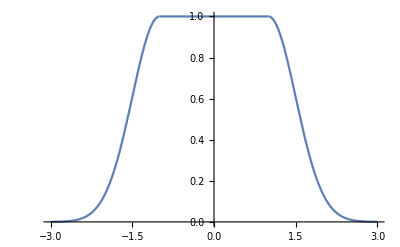

```mathematica
Θ[x_]:=HeavisideTheta[x];
yP=-1;yT=1;σ=1/2;
Plot[Exp[-Θ[-y+Min[{yP,yT}]] 1/(2 σ^2)(y-Min[{yP,yT}])^2-Θ[y-Max[{yP,yT}]] 1/(2 σ^2)(y-Max[{yP,yT}])^2],{y,-3,3}]
```

```mathematica
FourierTransform[Exp[-Θ[-y+Min[{yP,yT}]] 1/2(y-Min[{yP,yT}])^2-Θ[y-Max[{yP,yT}]] 1/2(y-Max[{yP,yT}])^2]/.{yP->-1,yT->1},y,k]
```

(ⅇ^(-1/2 k (2 ⅈ+k)) (2 ⅈ ⅇ^(k^2/2)-2 ⅈ ⅇ^(1/2 k (4 ⅈ+k))+k √(2 π)+ⅇ^(2 ⅈ k) k √(2 π)+ⅈ (-1+ⅇ^(2 ⅈ k)) k √(2 π) Erfi[k/(√2)]))/(2 k √(2 π))

```mathematica
Integrate[Exp[I α Sin[θ]+I ℓ θ],{θ,0,2π},Assumptions->α>0&&ℓ∈Integers]
```

Integrate[ⅇ^(ⅈ ℓ θ+ⅈ α Sin[θ]),{θ,0,2 π},Assumptions→α>0&&ℓ∈Integers]

```mathematica
ChebyshevT[2,Cos[θ]]//FullSimplify
ChebyshevT[2,Sin[θ]]//FullSimplify
```

Cos[2 θ]

-Cos[2 θ]

2 π BesselI[1,αC]

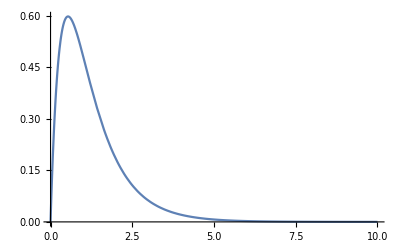

```mathematica
Integrate[Cos[3φ]Exp[αC Cos[3φ]],{φ,0,2π}]
Plot[Exp[-2α]2 π BesselI[1,α],{α,0,10}]
```